```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={r>0,z'[r]^2>0}
```

{r>0,z'[r]^2>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
CoordinateChartData["Spherical","Metric",{r,θ,φ}]
```

{{1,0,0},{0,r^2,0},{0,0,r^2 Sin[θ]^2}}

```mathematica
ΓMathematica = ResourceFunction["ChristoffelSymbol"][CoordinateChartData["Spherical","Metric",{r,θ,φ}],{r,θ,φ},"Kind"->"Second"]
```

{{{0,0,0},{0,-r,0},{0,0,-r Sin[θ]^2}},{{0,1/r,0},{1/r,0,0},{0,0,-Cos[θ] Sin[θ]}},{{0,0,1/r},{0,0,Cot[θ]},{1/r,Cot[θ],0}}}

```mathematica
(*ΓMathematica[[i, j, k]] = Γ^i_{k j}*)
```

```mathematica
Clear[Γ]
```

```mathematica
Γ[r_]:=
ResourceFunction["ChristoffelSymbol"][g[r], {r, θ}] // FullSimplify
```

```mathematica
(*\Nabla_r v^r*)
Δrvr[r_]:=v'[r]+v[r]Γ[r][[1,1,1]]
(*\Nabla_\theta v^theta*)
Δθvθ[r_]:=v[r]Γ[r][[2,2,1]]
```

```mathematica
Γ[r]
```

{{{(z'[r] z''[r])/(1+z'[r]^2),0},{0,-r/(1+z'[r]^2)}},{{0,1/r},{1/r,0}}}

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
```

```mathematica
N3dr[x_]:=-{Cos[x[[2]]], Sin[x[[2]]],0} 
N3dR[x_]:={Cos[x[[2]]], Sin[x[[2]]],0} 
N3dγ[x_]:={Cos[x[[2]]], Sin[x[[2]]],0}
```

```mathematica
Ntr[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dr[x].e[j][x],{j,1,2}],{i,1,2}]
NtR[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dR[x].e[j][x],{j,1,2}],{i,1,2}]
Ntγ[x_]:=Table[Sum[ig[x[[1]]][[i, j]] N3dγ[x].e[j][x],{j,1,2}],{i,1,2}]
```

```mathematica
Ntr[{r,θ}]//FullSimplify
NtR[{r,θ}]//FullSimplify
Ntγ[{r,θ}]//FullSimplify
```

{-1/(1+z'[r]^2),0}

{1/(1+z'[r]^2),0}

{1/(1+z'[r]^2),0}

```mathematica
nr[x_]:=Ntr[x]/Sqrt[Sum[Ntr[x][[i]] Ntr[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
nR[x_]:=NtR[x]/Sqrt[Sum[NtR[x][[i]] NtR[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
nγ[x_]:=Ntγ[x]/Sqrt[Sum[Ntγ[x][[i]] Ntγ[x][[j]] *g[x[[1]]][[i,j]],{i,1,2},{j,1,2}]]//FullSimplify
```

```mathematica
nγ[{r,θ}]
```

{√(1/(1+z'[r]^2)),0}

```mathematica
normal[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}]},{Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(*this is the function which appears under derivative in \Nalba_i \Nabla^i H*)
```

```mathematica
ϕ[r_]:=(r^2 H'[r])/sqrtdetg[r]
```

```mathematica
(* NablaNablaH = \Nalba_i \Nabla^i H*)
```

```mathematica
NablaNablaH[r_]:=1/sqrtdetg[r] ϕ'[r]
```

```mathematica
(*fVISC[r] = f^{VISC r}_notes*)
```

```mathematica
fVISCt[r_]:=(2 η (v''[r]+(v'[r] z'[r] z''[r])/(1+z'[r]^2)-(2 v[r] z'[r]^2 z''[r]^2)/((1+z'[r]^2)^2)+(v[r] z''[r]^2)/(1+z'[r]^2)+(-v[r]/r+v'[r]+(v[r] z'[r] z''[r])/(1+z'[r]^2))/r+(v[r] z'[r] Derivative[3][z][r])/(1+z'[r]^2)))/(1+z'[r]^2)
```

```mathematica
fσt[r_]:=ig[r][[1,1]]σ'[r]
```

```mathematica
fvt[r_]:=ρ v[r]Δrvr[r]
fvn[r_]:=ρ v[r]^2 b[r][[1,1]]
```

```mathematica
(*d[r][[i,j]] = d_{ij}_notes*)
```

```mathematica
d[r_]:={{g[r][[1,1]]Δrvr[r],0},{0,g[r][[2,2]]Δθvθ[r]}}
```

```mathematica
(*Π[r_][[i,j]]= \Pi^{ij}_notes*)
```

```mathematica
Π[r_]:=Table[Table[-σ[r]ig[r][[i,j]]-2 η ig[r][[i,i]]ig[r][[j,j]]d[r][[i,j]],{j,1,2}],{i,1,2}]
```

```mathematica
(*force per unit length exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlησt[r_]:=Table[Sum[Π[r][[i,j]] g[r][[j, k]]*nγ[{r,θ}][[k]],{j,1,2},{k,1,2}],{i,1,2}]
```

```mathematica
(*tangent force per unit length due to κ exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlκt[r_]:=Table[-2 κ H[r]^2 nγ[{r,θ}][[i]],{i,1,2}]
```

```mathematica
(*normal force per unit length due to κ exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlκn[r_]:=2 κ H'[r] nγ[{r,θ}][[1]]
```

```mathematica
(*tangent force per unit length, in the 3d space, due to σ and η exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlησ3d[r_,θ_]:=Sum[dFdlησt[r][[i]]e[i][{r,θ}],{i,1,2}]
```

```mathematica
(*tangent force per unit length, in the 3d space, due to κ exerted on the curve γ (circle centered at r=0) with normal nγ *)
```

```mathematica
dFdlκ3d[r_,θ_]:=Sum[dFdlκt[r][[i]]e[i][{r,θ}],{i,1,2}] +dFdlκn[r] normal[{r,θ}]
```

```mathematica
(*relation between v and z' given by the continuity equation*)
```

```mathematica
repv={v[r]->C1/(r √(1+(z'[r])^2)),v'[r]->-(C1 (1+z'[r]^2+r z'[r] z''[r]))/(r^2 (1+z'[r]^2)^(3/2)),v''[r]->(C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r Derivative[3][z][r])+r z'[r]^3 (2 z''[r]-r Derivative[3][z][r])))/(r^3 (1+z'[r]^2)^(5/2))};
```

```mathematica
Clear[dFdlησ3d]
dFdlησ3d[r_,θ_]:={(Cos[θ] (-σ[r]/(1+z'[r]^2)-(2 η ((C1 z'[r] z''[r])/(r (1+z'[r]^2)^(3/2))-(C1 (1+z'[r]^2+r z'[r] z''[r]))/(r^2 (1+z'[r]^2)^(3/2))))/(1+z'[r]^2)))/(√(1/(1+z'[r]^2))),(Sin[θ] (-σ[r]/(1+z'[r]^2)-(2 η ((C1 z'[r] z''[r])/(r (1+z'[r]^2)^(3/2))-(C1 (1+z'[r]^2+r z'[r] z''[r]))/(r^2 (1+z'[r]^2)^(3/2))))/(1+z'[r]^2)))/(√(1/(1+z'[r]^2))),(z'[r] (-σ[r]/(1+z'[r]^2)-(2 η ((C1 z'[r] z''[r])/(r (1+z'[r]^2)^(3/2))-(C1 (1+z'[r]^2+r z'[r] z''[r]))/(r^2 (1+z'[r]^2)^(3/2))))/(1+z'[r]^2)))/(√(1/(1+z'[r]^2)))}
```

```mathematica
Clear[dFdlκ3d]
dFdlκ3d[r_,θ_]:={-(κ Cos[θ] (1/(1+z'[r]^2))^(7/2) (z'[r]+z'[r]^3+r z''[r])^2)/(2 r^2)-(2 κ Cos[θ] z'[r] √(1/(1+z'[r]^2)) ((r (z'[r]+z'[r]^3+r z''[r]))/((r^2 (1+z'[r]^2))^(3/2))-(3 r^2 (z'[r]+z'[r]^3+r z''[r]) (2 r (1+z'[r]^2)+2 r^2 z'[r] z''[r]))/(4 (r^2 (1+z'[r]^2))^(5/2))+(r^2 (2 z''[r]+3 z'[r]^2 z''[r]+r Derivative[3][z][r]))/(2 (r^2 (1+z'[r]^2))^(3/2))))/(√(1+z'[r]^2)),-(κ Sin[θ] (1/(1+z'[r]^2))^(7/2) (z'[r]+z'[r]^3+r z''[r])^2)/(2 r^2)-(2 κ Sin[θ] z'[r] √(1/(1+z'[r]^2)) ((r (z'[r]+z'[r]^3+r z''[r]))/((r^2 (1+z'[r]^2))^(3/2))-(3 r^2 (z'[r]+z'[r]^3+r z''[r]) (2 r (1+z'[r]^2)+2 r^2 z'[r] z''[r]))/(4 (r^2 (1+z'[r]^2))^(5/2))+(r^2 (2 z''[r]+3 z'[r]^2 z''[r]+r Derivative[3][z][r]))/(2 (r^2 (1+z'[r]^2))^(3/2))))/(√(1+z'[r]^2)),-(κ z'[r] (1/(1+z'[r]^2))^(7/2) (z'[r]+z'[r]^3+r z''[r])^2)/(2 r^2)+(2 κ √(1/(1+z'[r]^2)) ((r (z'[r]+z'[r]^3+r z''[r]))/((r^2 (1+z'[r]^2))^(3/2))-(3 r^2 (z'[r]+z'[r]^3+r z''[r]) (2 r (1+z'[r]^2)+2 r^2 z'[r] z''[r]))/(4 (r^2 (1+z'[r]^2))^(5/2))+(r^2 (2 z''[r]+3 z'[r]^2 z''[r]+r Derivative[3][z][r]))/(2 (r^2 (1+z'[r]^2))^(3/2))))/(√(1+z'[r]^2))}
```

```mathematica
dFdltot3d[r_,θ_]:=dFdlησ3d[r,θ]+dFdlκ3d[r,θ]
```

```mathematica
FullSimplify[D[D[C1/(r √(1+(z'[r])^2)),r],r],Assumptions->ass]
```

(C1 (2+2 z'[r]^4-r^2 z''[r]^2+2 z'[r]^2 (2+r^2 z''[r]^2)+r z'[r] (2 z''[r]-r z^(3)[r])+r z'[r]^3 (2 z''[r]-r z^(3)[r])))/(r^3 (1+z'[r]^2)^(5/2))

```mathematica
eqs=FullSimplify[{   
ρ v[r]Δrvr[r]==ig[r][[1,1]]σ'[r]+2 η ig[r][[1,1]]( (D[Δrvr[r],r])+(Δrvr[r]-Δθvθ[r])Γ[r][[2,2,1]]),
ρ (v[r]^2) b[r][[1,1]]== κ(-2 NablaNablaH[r] -4H[r](H[r]^2-K[r]))+2 σ[r] H[r] +2 η (ig[r][[1,1]]Δrvr[r]b[r][[1,1]] + ig[r][[2,2]]Δθvθ[r]b[r][[2,2]])
},Assumptions->ass]
```

```mathematica
eqs=FullSimplify[eqs/.repv,Assumptions->ass]
```

```mathematica
(*T = nγ_i dFdlησt^i*)
```

```mathematica
T[r_]:=Sum[nγ[{r,θ}][[i]] g[r][[i,j]]dFdlησt[r][[j]],{i,1,2},{j,1,2}]//FullSimplify
```

```mathematica
Clear[κ,η,ρ]
```

```mathematica
Clear[C1]
```

```mathematica
(*
To produce figure-7:
Rmin=1/100;
Rmax=25/100;
κ=3*^-2;
η=1*^-2;
ρ=1*^-12;
vRmin=-1;
σRmax=1;
zRmax=0;
zpRmin=1/10;
zpRmax=0;
zRmin=-0.003809445308575343;

*)
```

```mathematica
Rmin=1;
Rmax=2;
```

```mathematica
κ=1;
η=1;
ρ=1;
```

```mathematica
(*values to be entered in variational+problem_bc_ring.py:
-vRmin = v_r_const_{variational+problem_bc_ring.py}
 -σRmax = sigma_R_const_{variational+problem_bc_ring.py}
- zRmax = z_R_const_{variational+problem_bc_ring.py}
- zpRmin = omega_r_const_{variational+problem_bc_ring.py}
- zpRmax = omega_R_const_{variational+problem_bc_ring.py}
*)
vRmin=1;
σRmax=0;
zRmax=0;
zpRmin=1;
zpRmax=0;
```

```mathematica
zRmin=-0.666253228077814;
```

```mathematica
solC1=Solve[vRmin==C1/(Rmin √(1+zpRmin^2)),C1][[1]]
```

{C1→√2}

```mathematica
C1=C1/.solC1
```

√2

```mathematica
(H[r]/.{r->Rmax}/.{z'[Rmax]->zpRmax})//FullSimplify
```

z''[2]/2

```mathematica
bcs=FullSimplify[{
σ[Rmax]==σRmax,
z[Rmin]==zRmin,z[Rmax]==zRmax,z'[Rmin]==zpRmin,z'[Rmax]==zpRmax
}];
```

```mathematica
bcs
```

{σ[2]==0,z[1]==-0.66059,z[2]==0,z'[1]==1,z'[2]==0}

```mathematica
sol=NDSolve[Flatten[{eqs,bcs}],{σ,z},{r,Rmin,Rmax},WorkingPrecision->30][[1]]
```

NDSolve::precw: The precision of the differential equation ({{σ'[r]/(1+Power[«2»])+(√2 (Power[«2»] Power[«2»]+2 r («1»)^(«1»)[«1»] Power[«2»] («1»)^(«1»)[«1»]))/r^3==0,«5»,z'[2]==0},{},{},{},{}}) is less than WorkingPrecision (30.).

{σ→InterpolatingFunction[…],z→InterpolatingFunction[…]}

```mathematica
vRmax= v[r]/.repv/.sol/.{r->Rmax}
```

0.70710678118654752440084436210484903928483593768847403658834

```mathematica
delta =1/100;
```

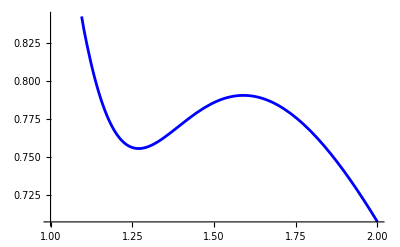

```mathematica
plotvODE=Plot[{v[r]/.repv/.sol},{r,Rmin,Rmax},PlotStyle->Blue]
```

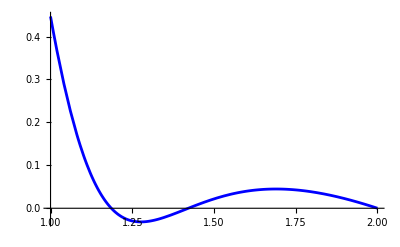

```mathematica
plotσODE=Plot[Evaluate[σ[r]/. sol],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Blue]
```

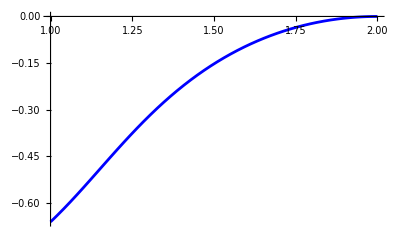

```mathematica
plotzODE=Plot[Evaluate[z[r]/. sol],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Blue]
```

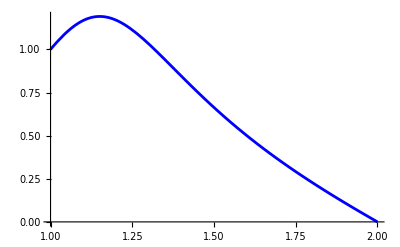

```mathematica
plotωODE=Plot[z'[r]/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

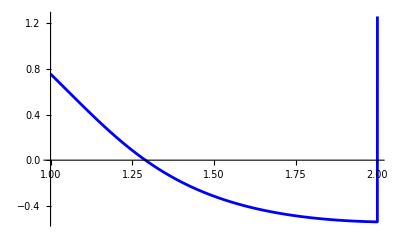

```mathematica
plotμODE=Plot[H[r]/.sol,{r,Rmin,Rmax},PlotStyle->Blue]
```

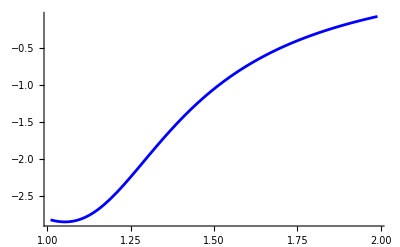

```mathematica
plotνexact=Plot[Evaluate[H'[r]/. sol],{r,Rmin+delta,Rmax-delta},PlotRange->All,PlotStyle->Blue]
```

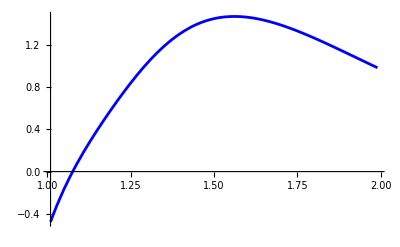

```mathematica
plotτexact=Plot[Evaluate[NablaNablaH[r]/. sol],{r,Rmin+delta,Rmax-delta},PlotRange->All,PlotStyle->Blue]
```

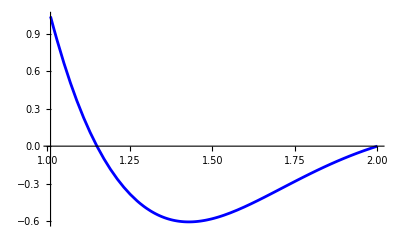

```mathematica
plotfVISCtexact=Plot[Evaluate[fVISCt[r]/.repv/.sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

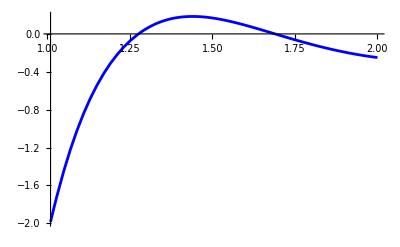

```mathematica
plotfσtexact=Plot[Evaluate[fσt[r]/.repv/.sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

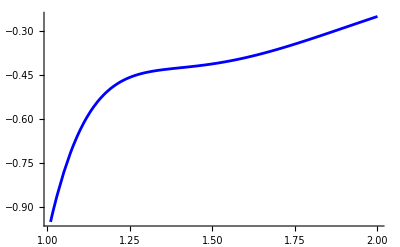

```mathematica
plotfvtexact=Plot[Evaluate[fvt[r]/.repv/.sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Blue]
```

```mathematica
(*plotftottexact=Plot[Evaluate[(fvt[r]-fσt[r]-fVISCt[r])/.repv/.sol],{r,Rmin+delta,Rmax},PlotRange->All,PlotStyle->Gray]*)
```

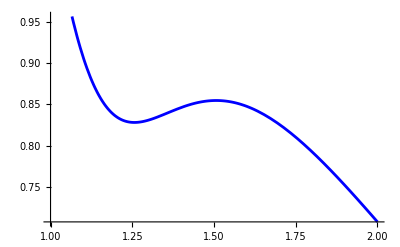

```mathematica
plotdFdlησtexact=  Plot[Evaluate[dFdlησt[r][[1]]/.repv/.sol],{r,Rmin,Rmax},PlotStyle->Blue]
```

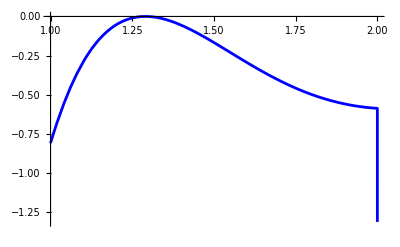

```mathematica
plotdFdlκtexact=  Plot[Evaluate[dFdlκt[r][[1]]/.repv/.sol],{r,Rmin,Rmax},PlotStyle->Blue]
```

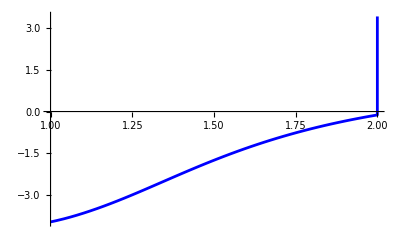

```mathematica
plotdFdlκnexact=  Plot[Evaluate[dFdlκn[r]/.repv/.sol],{r,Rmin,Rmax},PlotStyle->Blue]
```

```mathematica
plotdFdlησ3dexact={ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlησ3d[r,θ][[1]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlησ3d[r,θ][[2]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlησ3d[r,θ][[3]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
plotdFdlκ3dexact={ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlκ3d[r,θ][[1]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlκ3d[r,θ][[2]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdlκ3d[r,θ][[3]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
plotdFdltot3dexact={ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdltot3d[r,θ][[1]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdltot3d[r,θ][[2]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}],
ParametricPlot3D[{r Cos[θ],r Sin[θ],dFdltot3d[r,θ][[3]]/.sol},{r,Rmin,Rmax},{θ,0,2π},PlotStyle->{Opacity[0.1]},AxesLabel->{"x","y","z"},BoxRatios->{1,1,1}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(*Compare with the solution from FE*)
```

```mathematica
(*check of v*)
```

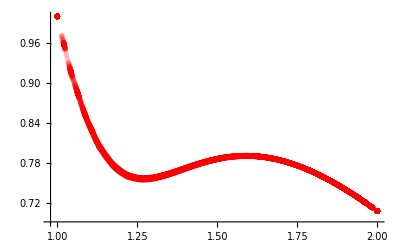

```mathematica
tabv=Import["~/Documents/finite_elements/steady-state-flow/solution/v.csv"];
tabv=Table[{Norm[{tabv[[i,4]],tabv[[i,5]]}],({tabv[[i,4]],tabv[[i,5]]}/Norm[{tabv[[i,4]],tabv[[i,5]]}]).{tabv[[i,1]],tabv[[i,2]]}},{i,2,Length[tabv]}]
plotvfe=ListPlot[tabv,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

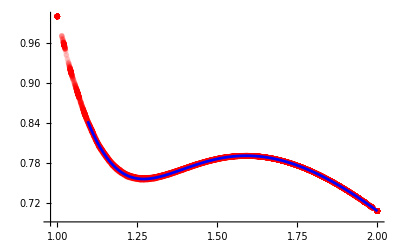

```mathematica
Show[plotvfe,plotvODE]
```

```mathematica
(*check of sigma*)
```

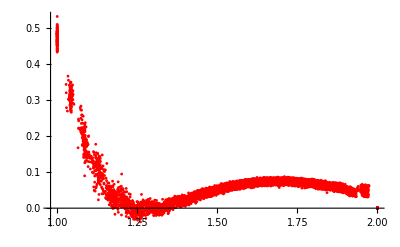

```mathematica
tabσ=Import["~/Documents/finite_elements/steady-state-flow/solution/sigma.csv"];
tabσ=Table[{Norm[{tabσ[[i,2]],tabσ[[i,3]]}],tabσ[[i,1]]},{i,2,Length[tabσ]}]
plotσfe=ListPlot[tabσ,PlotRange->Full,PlotStyle->{PointSize->.005,Red,Opacity[1]}]
```

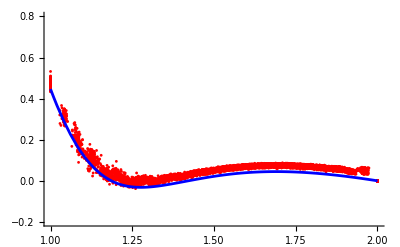

```mathematica
Show[plotσfe,plotσODE,PlotRange->{-0.2,0.8}]
```

```mathematica
(*check of z*)
```

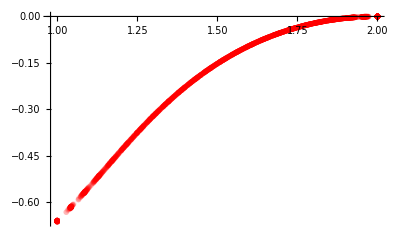

```mathematica
tabz=Import["~/Documents/finite_elements/steady-state-flow/solution/z.csv"];
tabz=Table[{Norm[{tabz[[i,2]],tabz[[i,3]]}],tabz[[i,1]]},{i,2,Length[tabz]}]
plotzfe=ListPlot[tabz,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

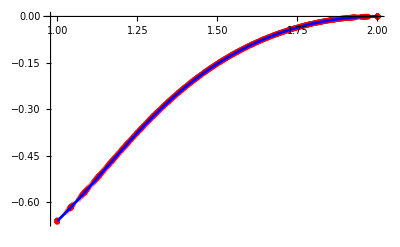

```mathematica
Show[plotzfe,plotzODE]
```

```mathematica
(*check of ω*)
```

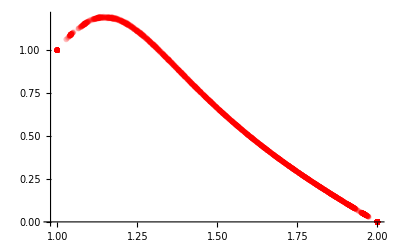

```mathematica
tabω=Import["~/Documents/finite_elements/steady-state-flow/solution/omega.csv"];
tabω=Table[{Norm[{tabω[[i,4]],tabω[[i,5]]}],({tabω[[i,4]],tabω[[i,5]]}/Norm[{tabω[[i,4]],tabω[[i,5]]}]).{tabω[[i,1]],tabω[[i,2]]}},{i,2,Length[tabω]}]
plotωfe=ListPlot[tabω,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

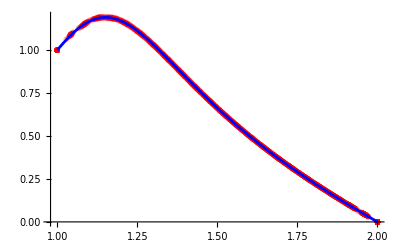

```mathematica
Show[plotωfe,plotωODE]
```

```mathematica
(*check of μ*)
```

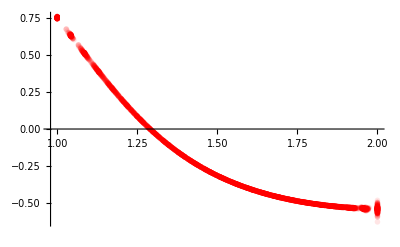

```mathematica
tabμ=Import["~/Documents/finite_elements/steady-state-flow/solution/mu.csv"];
tabμ=Table[{Norm[{tabμ[[i,2]],tabμ[[i,3]]}],tabμ[[i,1]]},{i,2,Length[tabμ]}]
plotμfe=ListPlot[tabμ,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

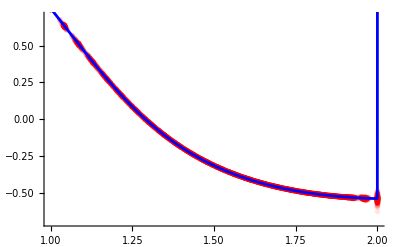

```mathematica
Show[plotμfe,plotμODE,PlotRange->{-0.7,0.7}]
```

```mathematica
(*check τ*)
```

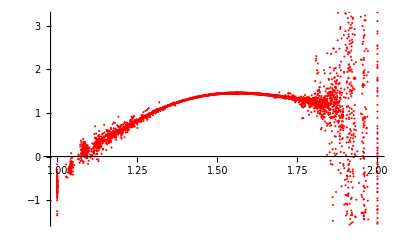

```mathematica
τnum=Import["~/Documents/finite_elements/steady-state-flow/solution/tau.csv"];
τnum=Table[{Sqrt[τnum[[i,2]]^2+τnum[[i,3]]^2],τnum[[i,1]]},{i,2,Length[τnum]}]
plotτnum=ListPlot[τnum,PlotStyle->{Red,Opacity->1}]
```

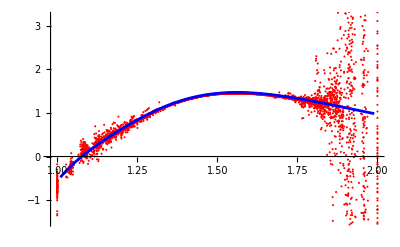

```mathematica
Show[plotτnum,plotτexact]
```

```mathematica
(*check of forces*)
```

```mathematica
(*normal forces*)
```

```mathematica
tabfeln=Import["~/Documents/finite_elements/steady-state-flow/solution/fel_n.csv"];
tabfeln=Table[{Norm[{tabfeln[[i,2]],tabfeln[[i,3]]}],tabfeln[[i,1]]},{i,2,Length[tabfeln]}]
```

```mathematica
tabflaplacen=Import["~/Documents/finite_elements/steady-state-flow/solution/flaplace.csv"];
tabflaplacen=Table[{Norm[{tabflaplacen[[i,2]],tabflaplacen[[i,3]]}],tabflaplacen[[i,1]]},{i,2,Length[tabflaplacen]}]
```

```mathematica
tabfviscn=Import["~/Documents/finite_elements/steady-state-flow/solution/fvisc_n.csv"];
tabfviscn=Table[{Norm[{tabfviscn[[i,2]],tabfviscn[[i,3]]}],tabfviscn[[i,1]]},{i,2,Length[tabfviscn]}]
```

```mathematica
tabconvcnn=Import["~/Documents/finite_elements/steady-state-flow/solution/conv_cn_n.csv"];
tabconvcnn=Table[{Norm[{tabconvcnn[[i,2]],tabconvcnn[[i,3]]}],-tabconvcnn[[i,1]]},{i,2,Length[tabconvcnn]}]
```

```mathematica
tabftotn=Table[{tabfviscn[[i,1]],tabfeln[[i,2]]+tabflaplacen[[i,2]]+tabfviscn[[i,2]]+tabconvcnn[[i,2]]},{i,2,Length[tabfviscn]}]
```

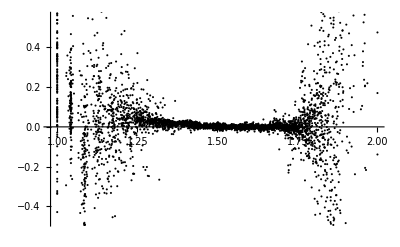

```mathematica
ListPlot[tabftotn,PlotStyle->Black]
```

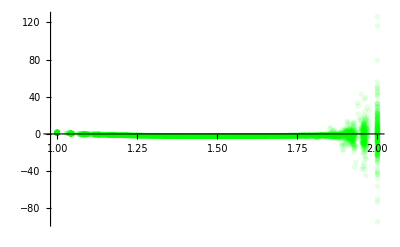

```mathematica
plotfeln=ListPlot[tabfeln,PlotRange->Full,PlotStyle->{PointSize->.01,Green,Opacity[0.1]}]
```

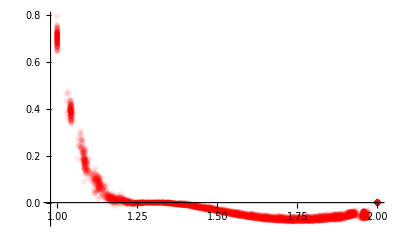

```mathematica
plotflaplacen=ListPlot[tabflaplacen,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

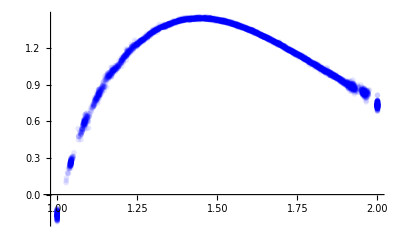

```mathematica
plotfviscn=ListPlot[tabfviscn,PlotRange->Full,PlotStyle->{PointSize->.01,Blue,Opacity[0.1]}]
```

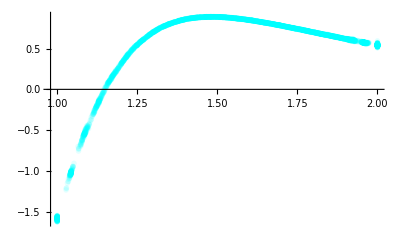

```mathematica
plotconvcnn=ListPlot[tabconvcnn,PlotRange->Full,PlotStyle->{PointSize->.01,Cyan,Opacity[0.1]}]
```

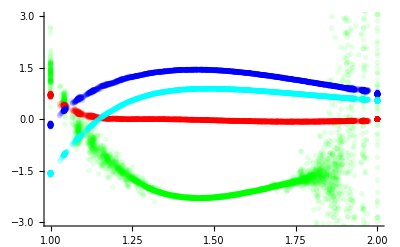

```mathematica
Show[plotfeln,plotflaplacen,plotfviscn,plotconvcnn,PlotRange->{-3,3}]
```

```mathematica
(*tangential forces*)
```

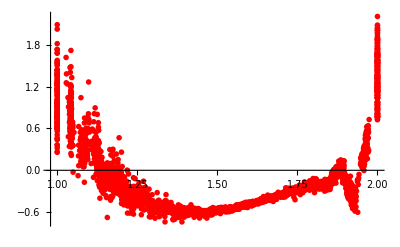

```mathematica
tabfVISCt=Import["~/Documents/finite_elements/steady-state-flow/solution/fvisc_t.csv"];
tabfVISCt=Table[{Norm[{tabfVISCt[[i,4]],tabfVISCt[[i,5]]}],({tabfVISCt[[i,4]],tabfVISCt[[i,5]]}/Norm[{tabfVISCt[[i,4]],tabfVISCt[[i,5]]}]).{tabfVISCt[[i,1]],tabfVISCt[[i,2]]}},{i,2,Length[tabfVISCt]}]
plotfVISCtfe=ListPlot[tabfVISCt,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[1]}]
```

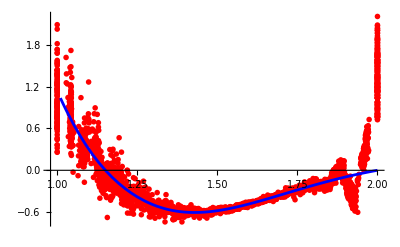

```mathematica
Show[plotfVISCtfe,plotfVISCtexact]
```

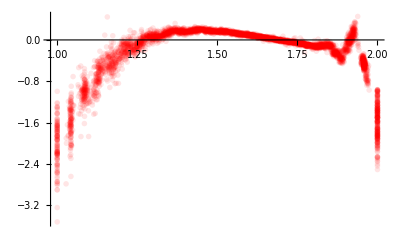

```mathematica
tabfσt=Import["~/Documents/finite_elements/steady-state-flow/solution/fsigma_t.csv"];
tabfσt=Table[{Norm[{tabfσt[[i,4]],tabfσt[[i,5]]}],({tabfσt[[i,4]],tabfσt[[i,5]]}/Norm[{tabfσt[[i,4]],tabfσt[[i,5]]}]).{tabfσt[[i,1]],tabfσt[[i,2]]}},{i,2,Length[tabfσt]}]
plotfσtfe=ListPlot[tabfσt,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

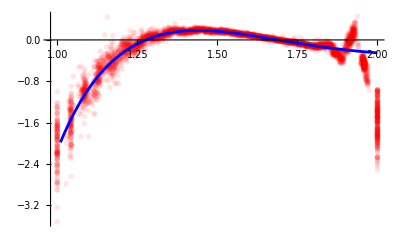

```mathematica
Show[plotfσtfe,plotfσtexact]
```

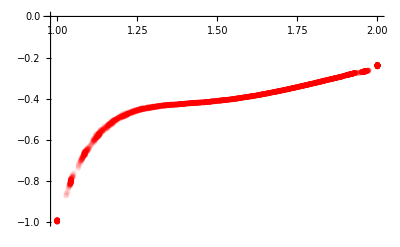

```mathematica
tabfvt=Import["~/Documents/finite_elements/steady-state-flow/solution/fv_t.csv"];
tabfvt=Table[{Norm[{tabfvt[[i,4]],tabfvt[[i,5]]}],({tabfvt[[i,4]],tabfvt[[i,5]]}/Norm[{tabfvt[[i,4]],tabfvt[[i,5]]}]).{tabfvt[[i,1]],tabfvt[[i,2]]}},{i,2,Length[tabfvt]}]
plotfvtfe=ListPlot[tabfvt,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

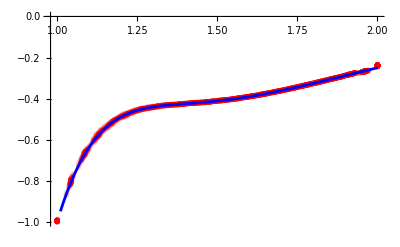

```mathematica
Show[plotfvtfe,plotfvtexact]
```

```mathematica
(*check that the sum fVISCt + fσt- fvt = 0*)
```

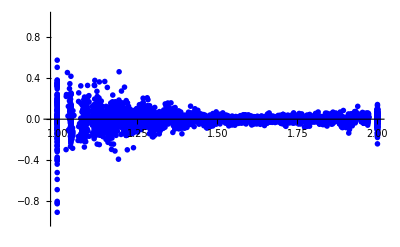

```mathematica
tabfVISCt=Import["~/Documents/finite_elements/steady-state-flow/solution/fvisc_t.csv"];
tabfσt=Import["~/Documents/finite_elements/steady-state-flow/solution/fsigma_t.csv"];
tabfvt=Import["~/Documents/finite_elements/steady-state-flow/solution/fv_t.csv"];
tabftott=Table[{Norm[{tabfVISCt[[i,4]],tabfVISCt[[i,5]]}],({tabfVISCt[[i,4]],tabfvt[[i,5]]}/Norm[{tabfVISCt[[i,4]],tabfVISCt[[i,5]]}]).{tabfVISCt[[i,1]]+tabfσt[[i,1]]-tabfvt[[i,1]],tabfVISCt[[i,2]]+tabfσt[[i,2]]-tabfvt[[i,2]]}},{i,2,Length[tabfVISCt]}]
plotftottfe=ListPlot[tabftott,PlotRange->{-1,1},PlotStyle->{PointSize->.01,Blue,Opacity[1]}]
```

```mathematica
(*force exerted on a line element, dFdlησt*)
```

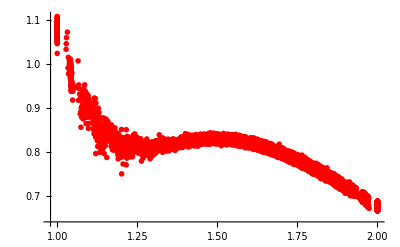

```mathematica
tabdFdlησt=Import["~/Documents/finite_elements/steady-state-flow/solution/dFdl_eta_sigma_t.csv"];
tabdFdlησt=Table[{Norm[{tabdFdlησt[[i,4]],tabdFdlησt[[i,5]]}],({tabdFdlησt[[i,4]],tabdFdlησt[[i,5]]}/Norm[{tabdFdlησt[[i,4]],tabdFdlησt[[i,5]]}]).{tabdFdlησt[[i,1]],tabdFdlησt[[i,2]]}},{i,2,Length[tabdFdlησt]}]
plotdFdlησtfe=ListPlot[tabdFdlησt,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[1]}]
```

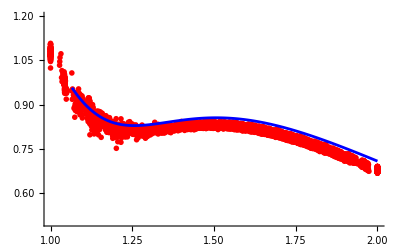

```mathematica
Show[plotdFdlησtfe,plotdFdlησtexact,PlotRange->{0.5,1.2}]
```

```mathematica
(*tangent force due to bending rigidity  exerted on a line element, dFdlκt*)
```

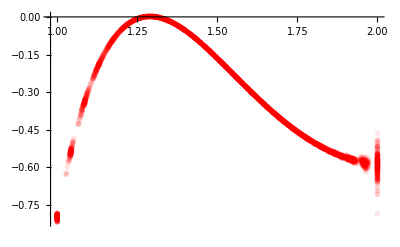

```mathematica
tabdFdlκt=Import["~/Documents/finite_elements/steady-state-flow/solution/dFdl_kappa_t.csv"];
tabdFdlκt=Table[{Norm[{tabdFdlκt[[i,4]],tabdFdlκt[[i,5]]}],({tabdFdlκt[[i,4]],tabdFdlκt[[i,5]]}/Norm[{tabdFdlκt[[i,4]],tabdFdlκt[[i,5]]}]).{tabdFdlκt[[i,1]],tabdFdlκt[[i,2]]}},{i,2,Length[tabdFdlκt]}]
plotdFdlκt=ListPlot[tabdFdlκt,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[0.1]}]
```

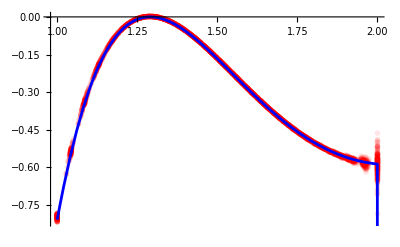

```mathematica
Show[plotdFdlκt,plotdFdlκtexact]
```

```mathematica
(*normal force due to bending rigidity  exerted on a line element, dFdlκn*)
```

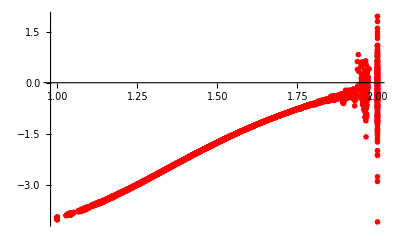

```mathematica
tabdFdlκn=Import["~/Documents/finite_elements/steady-state-flow/solution/dFdl_kappa_n.csv"];
tabdFdlκn=Table[{Norm[{tabdFdlκn[[i,2]],tabdFdlκn[[i,3]]}],tabdFdlκn[[i,1]]},{i,2,Length[tabdFdlκn]}]
plotdFdlκn=ListPlot[tabdFdlκn,PlotRange->Full,PlotStyle->{PointSize->.01,Red,Opacity[1]}]
```

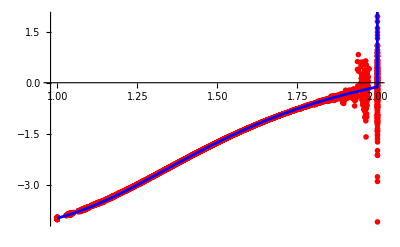

```mathematica
Show[plotdFdlκn,plotdFdlκnexact]
```

```mathematica
(*test forces per unit length in 3d space*)
```

```mathematica
(*check tabdFdlησ3d*)
tabdFdlησ3d=Import["~/Documents/finite_elements/steady-state-flow/solution/nodal_values/dFdl_eta_sigma_3d.csv"];
tabdFdlησ3d={Table[{tabdFdlησ3d[[i,4]],tabdFdlησ3d[[i,5]],tabdFdlησ3d[[i,1]]},{i,2,Length[tabdFdlησ3d]}],
Table[{tabdFdlησ3d[[i,4]],tabdFdlησ3d[[i,5]],tabdFdlησ3d[[i,2]]},{i,2,Length[tabdFdlησ3d]}],
Table[{tabdFdlησ3d[[i,4]],tabdFdlησ3d[[i,5]],tabdFdlησ3d[[i,3]]},{i,2,Length[tabdFdlησ3d]}]};
plottabdFdlησ3dfe={
ListPointPlot3D[tabdFdlησ3d[[1]],PlotRange->Full,PlotStyle->{PointSize->.005,Black,Opacity[1]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdlησ3d[[2]],PlotRange->Full,PlotStyle->{PointSize->.005,Black,Opacity[1]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdlησ3d[[3]],PlotRange->Full,PlotStyle->{PointSize->.005,Black,Opacity[1]},AxesLabel->{"x","y","z"}]}
Show[plotdFdlησ3dexact[[1]],plottabdFdlησ3dfe[[1]]]
Show[plotdFdlησ3dexact[[2]],plottabdFdlησ3dfe[[2]]]
Show[plotdFdlησ3dexact[[3]],plottabdFdlησ3dfe[[3]]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(*check tabdFdlκ3d*)
tabdFdlκ3d=Import["~/Documents/finite_elements/steady-state-flow/solution/nodal_values/dFdl_kappa_3d.csv"];
tabdFdlκ3d={Table[{tabdFdlκ3d[[i,4]],tabdFdlκ3d[[i,5]],tabdFdlκ3d[[i,1]]},{i,2,Length[tabdFdlκ3d]}],
Table[{tabdFdlκ3d[[i,4]],tabdFdlκ3d[[i,5]],tabdFdlκ3d[[i,2]]},{i,2,Length[tabdFdlκ3d]}],
Table[{tabdFdlκ3d[[i,4]],tabdFdlκ3d[[i,5]],tabdFdlκ3d[[i,3]]},{i,2,Length[tabdFdlκ3d]}]};
plottabdFdlκ3dfe={
ListPointPlot3D[tabdFdlκ3d[[1]],PlotRange->Full,PlotStyle->{PointSize->.005,Black,Opacity[1]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdlκ3d[[2]],PlotRange->Full,PlotStyle->{PointSize->.005,Black,Opacity[1]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdlκ3d[[3]],PlotRange->Full,PlotStyle->{PointSize->.005,Black,Opacity[1]},AxesLabel->{"x","y","z"}]}
Show[plotdFdlκ3dexact[[1]],plottabdFdlκ3dfe[[1]]]
Show[plotdFdlκ3dexact[[2]],plottabdFdlκ3dfe[[2]]]
Show[plotdFdlκ3dexact[[3]],plottabdFdlκ3dfe[[3]]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
(*check tabdFdltot3d*)
tabdFdltot3d=Import["~/Documents/finite_elements/steady-state-flow/solution/nodal_values/dFdl_tot_3d.csv"];
tabdFdltot3d={Table[{tabdFdltot3d[[i,4]],tabdFdltot3d[[i,5]],tabdFdltot3d[[i,1]]},{i,2,Length[tabdFdltot3d]}],
Table[{tabdFdltot3d[[i,4]],tabdFdltot3d[[i,5]],tabdFdltot3d[[i,2]]},{i,2,Length[tabdFdltot3d]}],
Table[{tabdFdltot3d[[i,4]],tabdFdltot3d[[i,5]],tabdFdltot3d[[i,3]]},{i,2,Length[tabdFdltot3d]}]};
plottabdFdltot3dfe={
ListPointPlot3D[tabdFdltot3d[[1]],PlotRange->Full,PlotStyle->{PointSize->.005,Black,Opacity[1]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdltot3d[[2]],PlotRange->Full,PlotStyle->{PointSize->.005,Black,Opacity[1]},AxesLabel->{"x","y","z"}],
ListPointPlot3D[tabdFdltot3d[[3]],PlotRange->Full,PlotStyle->{PointSize->.005,Black,Opacity[1]},AxesLabel->{"x","y","z"}]}
Show[plotdFdltot3dexact[[1]],plottabdFdltot3dfe[[1]]]
Show[plotdFdltot3dexact[[2]],plottabdFdltot3dfe[[2]]]
Show[plotdFdltot3dexact[[3]],plottabdFdltot3dfe[[3]]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

-Graphics3D-

-Graphics3D-

-Graphics3D-

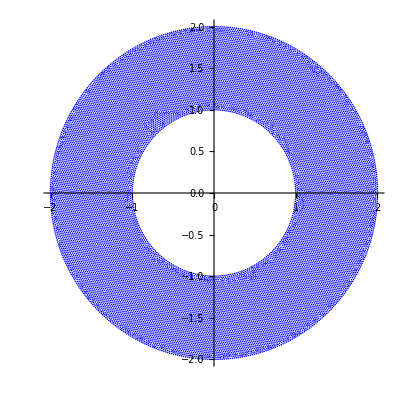

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/mesh/solution/vertices.csv"];
tabve=Drop[tabve,{1}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
```

```mathematica
(*write v from ODE to csv file*)
```

```mathematica
tabz=Table[{v[r]/.repv/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabz,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/v_ode.csv",tabz]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/v_ode.csv

```mathematica
(*write w==0 to csv file*)
```

```mathematica
tabw=Table[{0,tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabw,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/w_ode.csv",tabw]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/w_ode.csv

```mathematica
(*write sigma from ODE to csv file*)
```

```mathematica
tabσ=Table[{σ[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabσ,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/sigma_ode.csv",tabσ]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/sigma_ode.csv

```mathematica
(*write z from ODE to csv file*)
```

```mathematica
tabz=Table[{z[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabz,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/z_ode.csv",tabz]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/z_ode.csv

```mathematica
(*write omega=z' from ODE to csv file*)
```

```mathematica
tabω=Table[{z'[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabω,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/omega_ode.csv",tabω]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/omega_ode.csv

```mathematica
(*write mu=H from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[r]/.sol/.{r->Norm[tabve[[i]]]},tabve[[i,1]],tabve[[i,2]],0},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

```mathematica
Export["/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/mu_ode.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady-state-flow/solution-ode/mu_ode.csv